```mathematica
f[x_,y_]:=x*E^-(x^2.+y^2.);
grad[x_,y_]:=D[f[s,t],{{s,t}}]/.{s->x,t->y};
hessian[x_,y_]:={{D[f[s,t],{s,2}],D[f[s,t],s,t]},{D[f[s,t],t,s],D[f[s,t],{t,2}]}}/.{s->x,t->y};

guess={-.5,.3};
nearness=10^-3;
iterlimit=100;
roof=f[guess[[1]],guess[[2]]];

(*The following is for postprocessing*)
paths={};
record={guess};
```

Nearness Achieved: possible minima at {-0.707138,0.000102933}

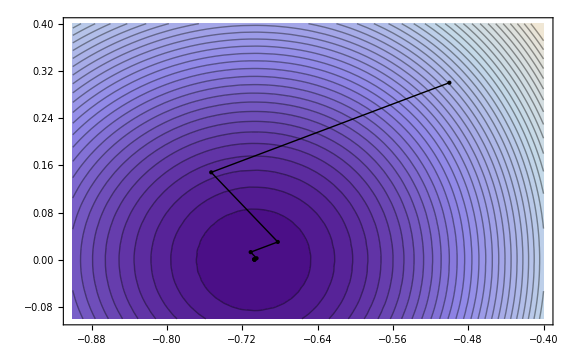

-Graphics3D-

```mathematica
For[i=1,i<iterlimit,i++,
old=guess;
(*path is the direction we're travelling*)
path[t_]:=guess-grad[guess[[1]],guess[[2]]]*t;
(*comp is the function evaluated at the path; f composed with γ in the notes*)
comp[t_]:=f[path[t][[1]],path[t][[2]]];
(*diff is the first derivative of f composed with γ*)
diff=D[comp[t],t];
(*travel the path until we are at an extrema*)
t0=FindRoot[diff,{t,0}][[1,2]];
(*post-processing:record a log of our travels*)
paths=Append[paths,{-grad[guess[[1]],guess[[2]]][[1]],-grad[guess[[1]],guess[[2]]][[2]],t0}];
(*travel the path to our new guess*)
guess=path[t0];
(*post-processing:record a log of our travels*)
record=Append[record,guess];

(*exit conditions*)
If[Norm[old-guess]<nearness,
Print["Nearness Achieved: possible minima at ",guess];
Break[];
];
If[f[guess[[1]],guess[[2]]]>roof,
Print["Wrong-way error: use a different initial guess"];
Break[];
];
]
(*POST PROCESSING*)
Show[ContourPlot[f[x,y],{x,-.9,-.4},{y,-.1,.4},Contours->40,AspectRatio->1/GoldenRatio,ImageSize->Large],Graphics[{Arrowheads[0],Arrow[record],PointSize[Large],Point[record]}]]
Show[Plot3D[f[x,y],{x,-.9,-.4},{y,-.1,.4},ImageSize->Large],Table[ParametricPlot3D[{record[[i]][[1]]+paths[[i]][[1]]t,record[[i]][[2]]+paths[[i]][[2]]t,f[record[[i]][[1]]+paths[[i]][[1]]t,record[[i]][[2]]+paths[[i]][[2]]t]},{t,0,paths[[i]][[3]]},PlotStyle->{Black,Thick}],{i,1,Length[record]-1}],Boxed->False]
```

Nearness Achieved: possible minima at {-0.707107,-1.59012×10^-8}

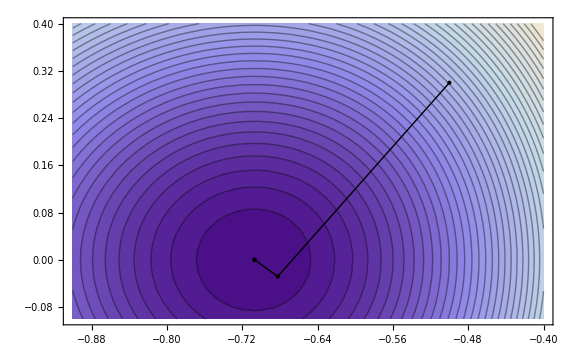

-Graphics3D-

```mathematica
For[i=1,i<iterlimit,i++,
old=guess;
(*path is the direction we're traveling*)
path[t_]:=guess+Inverse[hessian[guess[[1]],guess[[2]]]].grad[guess[[1]],guess[[2]]]*t;
(*comp is the function composed with the path; f composed with γ in the notes*)
comp[t_]:=f[path[t][[1]],path[t][[2]]];
(*diff is the first derivative of the composition*)
diff=D[comp[t],t];
(*t0 is how long we travel the path until we hit an extrema*)
t0=FindRoot[diff,{t,0}][[1,2]];
(*post-processing:record our travels*)
paths=Append[paths,{(Inverse[hessian[guess[[1]],guess[[2]]]].grad[guess[[1]],guess[[2]]])[[1]],(Inverse[hessian[guess[[1]],guess[[2]]]].grad[guess[[1]],guess[[2]]])[[2]],t0}];
(*travel down path until the extrema and set that as the next guess*)
guess=path[t0];
(*post-processing:record our travels*)
record=Append[record,guess];
(*exit conditions*)
If[Norm[old-guess]<nearness,
Print["Nearness Achieved: possible minima at ",guess];
Break[];
];
If[f[guess[[1]],guess[[2]]]>roof,
Print["Wrong-way error: use a different initial guess"];
Break[];
];
]
Show[ContourPlot[f[x,y],{x,-.9,-.4},{y,-.1,.4},Contours->40,AspectRatio->1/GoldenRatio,ImageSize->Large],Graphics[{Arrowheads[0],Arrow[record],PointSize[Large],Point[record]}]]
Show[Plot3D[f[x,y],{x,-.9,-.4},{y,-.1,.4},ImageSize->Large],Table[ParametricPlot3D[{record[[i]][[1]]+paths[[i]][[1]]t,record[[i]][[2]]+paths[[i]][[2]]t,f[record[[i]][[1]]+paths[[i]][[1]]t,record[[i]][[2]]+paths[[i]][[2]]t]},{t,0,paths[[i]][[3]]},PlotStyle->{Black,Thick}],{i,1,Length[record]-1}],Boxed->False]
```